```mathematica
Clear["Global`*"]
<<Combinatorica`
(*Quiet[<<Combinatorica`]*)
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
S=SparseArray[{
{1,2}-> 5,{1,3}-> 2,
{2,3}-> 3,
{3,1}-> 2,{3,4}-> 5,
{4,1}-> 6
},{4,4},Infinity];
S=Normal[S];
S//MatrixForm
```

(∞ | 5 | 2 | ∞
∞ | ∞ | 3 | ∞
2 | ∞ | ∞ | 5
6 | ∞ | ∞ | ∞)

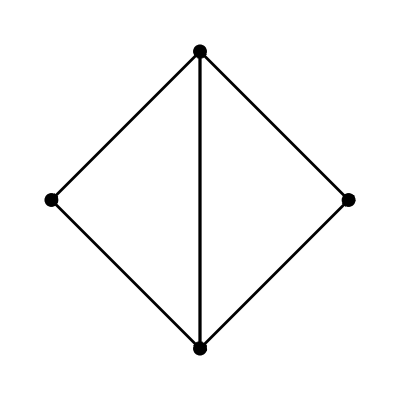

```mathematica
g1=FromAdjacencyMatrix[S,EdgeWeight,Type-> Directed];
ShowGraph[g1,VertexLabel -> True]
```

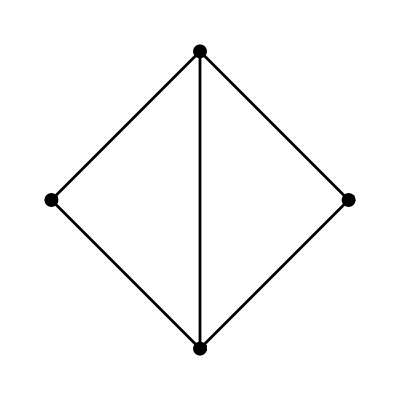

```mathematica
g2=FromAdjacencyMatrix[S,EdgeWeight];
ShowGraph[g2,VertexLabel -> True]
```

```mathematica
ShortestPath[g1,1,4]
```

{1,3,4}

```mathematica
S=SparseArray[{
{1,2}-> 5,{1,3}-> 10,{1,6}-> 6,
{2,3}-> 3,{2,5}-> 6,
{3,4}-> 2,{3,5}-> 3,{3,6}-> 4,
{4,5}-> 2,{4,6}-> 5
},{6,6},Infinity];
S=Normal[S];
S//MatrixForm
```

(∞ | 5 | 10 | ∞ | ∞ | 6
∞ | ∞ | 3 | ∞ | 6 | ∞
∞ | ∞ | ∞ | 2 | 3 | 4
∞ | ∞ | ∞ | ∞ | 2 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞)

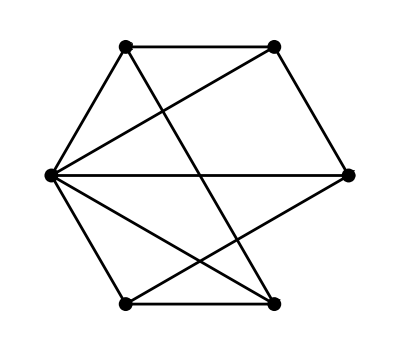

```mathematica
gs=FromAdjacencyMatrix[S,EdgeWeight];
ShowGraph[gs,VertexLabel -> True]
```

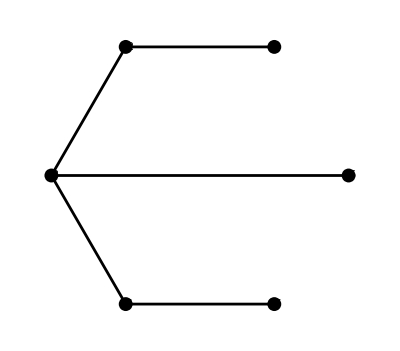

```mathematica
ShowGraph[MinimumSpanningTree[gs],VertexLabel -> True]
```

```mathematica
S=SparseArray[{
{1,2}-> 50,{1,3}-> 40,{1,6}-> 95,
{2,3}-> 45,{2,5}-> 120,
{3,4}-> 75,{3,5}-> 80,{3,6}-> 85,
{4,5}-> 25,{4,6}-> 30,{4,8}-> 30,
{5,7}-> 55, {5,8}-> 35,
{6,8}-> 75,
{7,8}-> 60
},{8,8},Infinity];
S=Normal[S];
S//MatrixForm
```

(∞ | 50 | 40 | ∞ | ∞ | 95 | ∞ | ∞
∞ | ∞ | 45 | ∞ | 120 | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 75 | 80 | 85 | ∞ | ∞
∞ | ∞ | ∞ | ∞ | 25 | 30 | ∞ | 30
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 55 | 35
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 75
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 60
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞)

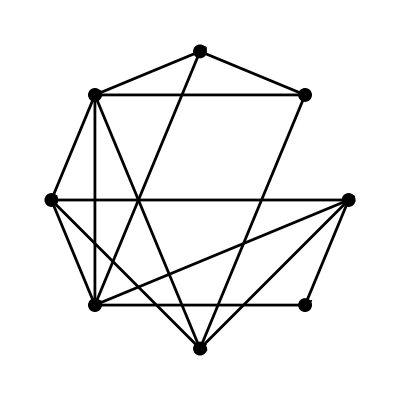

```mathematica
gus=FromAdjacencyMatrix[S,EdgeWeight];
ShowGraph[gus,VertexLabel -> True]
```

```mathematica
pus=ShortestPath[gus,1,8]
CostOfPath[gus,pus]
```

{1,3,4,8}

145

```mathematica
Table[{1,ShortestPath[gus,1,i]-> CostOfPath[gus,ShortestPath[gus,1,i]],i},{i,2,8}]//TableForm
```

1 | {1,2}→50 | 2
1 | {1,3}→40 | 3
1 | {1,3,4}→115 | 4
1 | {1,3,5}→120 | 5
1 | {1,6}→95 | 6
1 | {1,3,5,7}→175 | 7
1 | {1,3,4,8}→145 | 8